```mathematica
coords={{0,0},{0,z},{x,y},{-x,y}}
```

{{0,0},{0,z},{x,y},{-x,y}}

```mathematica
U[a_,b_]:=(Sqrt[a^2+b^2]-1)^2
```

```mathematica
u=Total[U@@@(#[[1]]-#[[2]]&/@Subsets[coords,{2}])]
```

(-1+2 √(x^2))^2+2 (-1+√(x^2+y^2))^2+(-1+√(z^2))^2+2 (-1+√(x^2+(-y+z)^2))^2

```mathematica
(D[u,#]==0)&/@{x,y,z}//FullSimplify
```

{x (4-1/(√(x^2+y^2))-1/(√(x^2+(y-z)^2)))==x/(√(x^2)),y (2-1/(√(x^2+y^2))-1/(√(x^2+(y-z)^2)))+(-1+1/(√(x^2+(y-z)^2))) z==0,z (3-1/(√(z^2)))==(2 (y (-1+√(x^2+(y-z)^2))+z))/(√(x^2+(y-z)^2))}

```mathematica
sol=Solve[And@@((D[u,#]==0&&#>0)&/@{x,y,z})]
```

{{x→1/4 √(3+2 √2),y→1/4 (1+√2),z→1/2 (1+√2)},{x→1/4 √(3/2 (2+√3)),y→1/736 √(135424+67712 √3) (1+92 √(3/(135424+67712 √3))+92/(√(135424+67712 √3))),z→1/4 (1+√3)}}

```mathematica
ssol=sol//FullSimplify
```

{{x→1/4 (1+√2),y→1/4 (1+√2),z→1/2+1/(√2)},{x→1/8 (3+√3),y→3/8 (1+√3),z→1/4 (1+√3)}}

```mathematica
u/.ssol[[1]]//FullSimplify
```

3-2 √2

```mathematica
u/.ssol[[2]]//FullSimplify
```

3-(3 √3)/2

```mathematica
Table[D[u,a,b],{a,{x,y,z}},{b,{x,y,z}}]/.ssol[[1]]//FullSimplify
Eigenvalues[%]//FullSimplify
%//N
```

{{8 √2,0,8-4 √2},{0,8 (-1+√2),4-4 √2},{8-4 √2,4-4 √2,-2+4 √2}}

{2 Root6.00Root[{-2+#1^2&,-192+128 #1+32 #2-8 #1 #2+5 #2^2-10 #1 #2^2+#2^3&},{2,3}]5.998935096301013,2 Root2.37Root[{-2+#1^2&,-192+128 #1+32 #2-8 #1 #2+5 #2^2-10 #1 #2^2+#2^3&},{2,2}]2.3712826047761104,2 Root0.772Root[{-2+#1^2&,-192+128 #1+32 #2-8 #1 #2+5 #2^2-10 #1 #2^2+#2^3&},{2,1}]0.7719179226538273}

{11.9979,4.74257,1.54384}

```mathematica
Table[D[u,a,b],{a,{x,y,z}},{b,{x,y,z}}]/.ssol[[2]]//FullSimplify
Eigenvalues[%]//FullSimplify
%//N
```

{{12,4,2 (-3+√3)},{4,12-16/(√3),-10+6 √3},{2 (-3+√3),-10+6 √3,-6 (-2+√3)}}

{18-17/(√3)+√(493/3-76 √3),18-17/(√3)-√(493/3-76 √3),0}

{13.9032,2.46688,0.}

```mathematica
Eigensystem[%245]//FullSimplify
```

{{18-17/(√3)+√(493/3-76 √3),18-17/(√3)-√(493/3-76 √3),0},{{Root-5.13Root[22+186 #1+361 #1^2+84 #1^3+4 #1^4&,2]-5.127964174452921,Root-1.81Root[162+90 #1-169 #1^2-72 #1^3+12 #1^4&,1]-1.8059309581358995,1},{1/4 (-21+6 √3+√(493-228 √3)),1/12 (18-13 √3+√(1479-684 √3)),1},{1/2,-(√3)/2,1}}}

```mathematica
u/.{x->1/8 (3+√3)+(1/2)e,y->3/8 (1+√3)-(Sqrt[3]/2)e,z->1/4 (1+√3)+e}//FullSimplify
```

(-1+√((1/4 (1+√3)+e)^2))^2+1/16 (-4+√((3+√3+4 e)^2))^2+1/8 (-4+√(6 (2+√3)-4 (3+√3) e+16 e^2))^2+1/8 (-4+√2 √(2+√3-2 (1+√3) e+8 (2+√3) e^2))^2

```mathematica
u/.{x->1/8 (3+√3),y->3/8 (1+√3),z->1/4 (1+√3)+e}//FullSimplify
```

1/4 (18+12 e^2-2 √((1+√3+4 e)^2)-4 √2 √(2+√3-2 (1+√3) e+8 e^2))

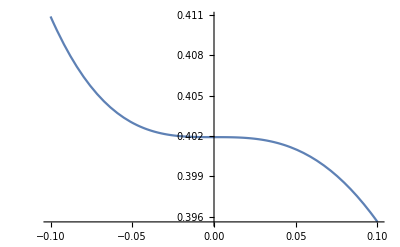

```mathematica
Plot[(-1+√((1/4 (1+√3)+e)^2))^2+1/16 (-4+√((3+√3+4 e)^2))^2+1/8 (-4+√(6 (2+√3)-4 (3+√3) e+16 e^2))^2+1/8 (-4+√2 √(2+√3-2 (1+√3) e+8 (2+√3) e^2))^2,{e,-.1,.1}]
```

```mathematica
Series[1/4 (18+12 e^2-2 √((1+√3+4 e)^2)-4 √2 √(2+√3-2 (1+√3) e+8 e^2)),{e,0,2}]//FullSimplify
```

(3-(3 √3)/2)+(6-3 √3) e^2+O[e]^3

```mathematica
Series[(-1+√((1/4 (1+√3)+e)^2))^2+1/16 (-4+√((3+√3+4 e)^2))^2+1/8 (-4+√(6 (2+√3)-4 (3+√3) e+16 e^2))^2+1/8 (-4+√2 √(2+√3-2 (1+√3) e+8 (2+√3) e^2))^2,{e,0,3}]//FullSimplify
```

(3-(3 √3)/2)-8 e^3+O[e]^4

```mathematica
coords={{0,0,0},{0,0,z},{0,x,y},{x Sqrt[3]/2,-x/2,y},{-x Sqrt[3]/2,-x/2,y}}
```

{{0,0,0},{0,0,z},{0,x,y},{(√3 x)/2,-x/2,y},{-(√3 x)/2,-x/2,y}}

```mathematica
U[a_,b_,c_]:=(Sqrt[a^2+b^2+c^2]-1)^2
```

```mathematica
u=Total[U@@@(#[[1]]-#[[2]]&/@Subsets[coords,{2}])]
```

3 (-1+√3 √(x^2))^2+3 (-1+√(x^2+y^2))^2+(-1+√(z^2))^2+3 (-1+√(x^2+(-y+z)^2))^2

```mathematica
(D[u,#]==0)&/@{x,y,z}//FullSimplify
```

{x (5-1/(√(x^2+y^2))-1/(√(x^2+(y-z)^2)))==(√3 x)/(√(x^2)),y (2-1/(√(x^2+y^2))-1/(√(x^2+(y-z)^2)))+(-1+1/(√(x^2+(y-z)^2))) z==0,z (4-1/(√(z^2)))==(3 (y (-1+√(x^2+(y-z)^2))+z))/(√(x^2+(y-z)^2))}

```mathematica
And@@((D[u,#]==0&&#>0)&/@{x,y,z})//FullSimplify
```

x (5-1/(√(x^2+y^2))-1/(√(x^2+(y-z)^2)))==√3&&x>0&&y (2-1/(√(x^2+y^2))-1/(√(x^2+(y-z)^2)))+(-1+1/(√(x^2+(y-z)^2))) z==0&&y>0&&1+(3 (y (-1+√(x^2+(y-z)^2))+z))/(√(x^2+(y-z)^2))==4 z&&z>0

```mathematica
sol=Solve[x (5-1/(√(x^2+y^2))-1/(√(x^2+(y-z)^2)))==√3&&x>0&&y (2-1/(√(x^2+y^2))-1/(√(x^2+(y-z)^2)))+(-1+1/(√(x^2+(y-z)^2))) z==0&&y>0&&1+(3 (y (-1+√(x^2+(y-z)^2))+z))/(√(x^2+(y-z)^2))==4 z&&z>0]
```

{{x→(2 (6+√6))/(15 √3),y→1/30 (3+3 √6+5 √(7+2 √6)),z→1/5 (1+√6)},{x→Root0.632Root[{-3+#1^2&,-16-752 #2+300 #2^2+100 #2^3+125 #2^4&,14485316357520 #1+445702903299904 #1 #2-502016496213120 #1 #2^2-4399433335364200 #1 #2^3+3625301138529000 #1 #2^4+8634280443020625 #1 #2^5-9326064641550000 #1 #2^6+1054450761593750 #1 #2^7-629712123750000 #1 #2^8+1048516823828125 #1 #2^9+301430193505488 #3&},{2,2,1}]0.6318325069801116,y→Root0.620Root[{-16-752 #1+300 #1^2+100 #1^3+125 #1^4&,36 #1+242 #1^2-165 #1^3-2000 #1^4+1250 #1^5+3750 #1^6-3125 #1^7-72 #2-484 #1 #2+330 #1^2 #2+4000 #1^3 #2-2500 #1^4 #2-7500 #1^5 #2+6250 #1^6 #2&},{2,1}]0.6203590020376807,z→Root1.24Root[-16-752 #1+300 #1^2+100 #1^3+125 #1^4&,2]1.2407180040753614},{x→Root0.618Root[{-3+#1^2&,36+170 #2-325 #2^2-500 #2^3+625 #2^4&,14485316357520 #1+445702903299904 #1 #2-502016496213120 #1 #2^2-4399433335364200 #1 #2^3+3625301138529000 #1 #2^4+8634280443020625 #1 #2^5-9326064641550000 #1 #2^6+1054450761593750 #1 #2^7-629712123750000 #1 #2^8+1048516823828125 #1 #2^9+301430193505488 #3&},{2,3,1}]0.6179315275766487,y→Root0.991Root[{36+170 #1-325 #1^2-500 #1^3+625 #1^4&,-476873395920-30015639140560 #1-332482952726216 #1^2-258910599398100 #1^3+1602063722093625 #1^4+278151107426250 #1^5-1769807589468750 #1^6+221730784937500 #1^7+59956784140625 #1^8+227393139843750 #1^9-100476731168496 #1 #2+100476731168496 #2^2&},{3,2}]0.9908279461241246,z→1/10 (2+√(2 (19-√145)))}}

```mathematica
ssol=sol//FullSimplify
```

{{x→(2 (6+√6))/(15 √3),y→4/15 (1+√6),z→1/5 (1+√6)},{x→Root0.632Root[{-3+#1^2&,-16-752 #2+300 #2^2+100 #2^3+125 #2^4&,14485316357520 #1+445702903299904 #1 #2-502016496213120 #1 #2^2-4399433335364200 #1 #2^3+3625301138529000 #1 #2^4+8634280443020625 #1 #2^5-9326064641550000 #1 #2^6+1054450761593750 #1 #2^7-629712123750000 #1 #2^8+1048516823828125 #1 #2^9+301430193505488 #3&},{2,2,1}]0.6318325069801116,y→Root0.620Root[{-16-752 #1+300 #1^2+100 #1^3+125 #1^4&,36 #1+242 #1^2-165 #1^3-2000 #1^4+1250 #1^5+3750 #1^6-3125 #1^7-72 #2-484 #1 #2+330 #1^2 #2+4000 #1^3 #2-2500 #1^4 #2-7500 #1^5 #2+6250 #1^6 #2&},{2,1}]0.6203590020376807,z→Root1.24Root[-16-752 #1+300 #1^2+100 #1^3+125 #1^4&,2]1.2407180040753614},{x→1/30 (8 √3+√(46-2 √145)),y→1/60 (6+3 √(38-2 √145)+√(10 (35+5 √145+4 √(615-15 √145)))),z→1/10 (2+√(38-2 √145))}}

```mathematica
({x/z,y/z}/.#)&/@ssol
```

{{(2 (6+√6))/(3 √3 (1+√6)),4/3},{(Root0.632Root[{-3+#1^2&,-16-752 #2+300 #2^2+100 #2^3+125 #2^4&,14485316357520 #1+445702903299904 #1 #2-502016496213120 #1 #2^2-4399433335364200 #1 #2^3+3625301138529000 #1 #2^4+8634280443020625 #1 #2^5-9326064641550000 #1 #2^6+1054450761593750 #1 #2^7-629712123750000 #1 #2^8+1048516823828125 #1 #2^9+301430193505488 #3&},{2,2,1}]0.6318325069801116)/(Root1.24Root[-16-752 #1+300 #1^2+100 #1^3+125 #1^4&,2]1.2407180040753614),(Root0.620Root[{-16-752 #1+300 #1^2+100 #1^3+125 #1^4&,36 #1+242 #1^2-165 #1^3-2000 #1^4+1250 #1^5+3750 #1^6-3125 #1^7-72 #2-484 #1 #2+330 #1^2 #2+4000 #1^3 #2-2500 #1^4 #2-7500 #1^5 #2+6250 #1^6 #2&},{2,1}]0.6203590020376807)/(Root1.24Root[-16-752 #1+300 #1^2+100 #1^3+125 #1^4&,2]1.2407180040753614)},{(8 √3+√(46-2 √145))/(3 (2+√(38-2 √145))),(6+3 √(38-2 √145)+√(10 (35+5 √145+4 √(615-15 √145))))/(6 (2+√(38-2 √145)))}}

```mathematica
%287//RootReduce
```

{{(2 √2)/3,4/3},{Root0.509Root[9+24 #1^2-144 #1^4-384 #1^6+256 #1^8&,3]0.5092474719515185,1/2},{Root1.08Root[62208-1928992 #1^2+3350763 #1^4-1860732 #1^6+314928 #1^8&,6]1.0783158843683192,Root1.73Root[288-457408 #1-108719 #1^2+1368126 #1^3-958815 #1^4-552096 #1^5+1653696 #1^6-1259712 #1^7+314928 #1^8&,6]1.7290354437355566}}

```mathematica
%289//N
```

{{0.942809,1.33333},{0.509247,0.5},{1.07832,1.72904}}

```mathematica
Table[D[Simplify[u],a,b],{a,{x,y,z}},{b,{x,y,z}}]/.ssol[[1]]//RootReduce
Eigenvalues[%]//Simplify
%//N
```

{{Root23.3Root[-4374000+9720 #1^2-96 #1^3+#1^4&,2]23.34810380651157,0,Root3.39Root[236196000000-20820240000 #1^2+20703600 #1^4-7992 #1^6+#1^8&,3]3.3874613202179122},{0,Root5.10Root[-15344640+2875392 #1+24192 #1^2+384 #1^3+#1^4&,2]5.0997755453819,Root-2.55Root[-959040-359424 #1+6048 #1^2-192 #1^3+#1^4&,1]-2.54988777269095},{Root3.39Root[236196000000-20820240000 #1^2+20703600 #1^4-7992 #1^6+#1^8&,3]3.3874613202179122,Root-2.55Root[-959040-359424 #1+6048 #1^2-192 #1^3+#1^4&,1]-2.54988777269095,Root4.55Root[-1655216+337504 #1+4920 #1^2+184 #1^3+#1^4&,2]4.54988777269095}}

{Root24.0Root[{-4374000+9720 #1^2-96 #1^3+#1^4&,-1655216+337504 #2+4920 #2^2+184 #2^3+#2^4&,-15344640+2875392 #3+24192 #3^2+384 #3^3+#3^4&,-959040-359424 #4+6048 #4^2-192 #4^3+#4^4&,236196000000-20820240000 #5^2+20703600 #5^4-7992 #5^6+#5^8&,-#1 #2 #3+#1 #4^2+#3 #5^2+#1 #2 #6+#1 #3 #6+#2 #3 #6-#4^2 #6-#5^2 #6-#1 #6^2-#2 #6^2-#3 #6^2+#6^3&},{2,2,2,1,3,3}]23.950287262176662,Root7.10Root[{-4374000+9720 #1^2-96 #1^3+#1^4&,-1655216+337504 #2+4920 #2^2+184 #2^3+#2^4&,-15344640+2875392 #3+24192 #3^2+384 #3^3+#3^4&,-959040-359424 #4+6048 #4^2-192 #4^3+#4^4&,236196000000-20820240000 #5^2+20703600 #5^4-7992 #5^6+#5^8&,-#1 #2 #3+#1 #4^2+#3 #5^2+#1 #2 #6+#1 #3 #6+#2 #3 #6-#4^2 #6-#5^2 #6-#1 #6^2-#2 #6^2-#3 #6^2+#6^3&},{2,2,2,1,3,2}]7.097849344618733,Root1.95Root[{-4374000+9720 #1^2-96 #1^3+#1^4&,-1655216+337504 #2+4920 #2^2+184 #2^3+#2^4&,-15344640+2875392 #3+24192 #3^2+384 #3^3+#3^4&,-959040-359424 #4+6048 #4^2-192 #4^3+#4^4&,236196000000-20820240000 #5^2+20703600 #5^4-7992 #5^6+#5^8&,-#1 #2 #3+#1 #4^2+#3 #5^2+#1 #2 #6+#1 #3 #6+#2 #3 #6-#4^2 #6-#5^2 #6-#1 #6^2-#2 #6^2-#3 #6^2+#6^3&},{2,2,2,1,3,1}]1.9496305177890256}

{23.9503,7.09785,1.94963}

```mathematica
(FullSimplify[u]/.#)&/@ssol
```

{(-1+1/5 (1+√6))^2+3 (-1+2/15 (6+√6))^2+3 (-1+√(16/225 (1+√6)^2+4/675 (6+√6)^2))^2+3 (-1+√(4/675 (6+√6)^2+(1/5 (-1-√6)+4/15 (1+√6))^2))^2,3 (-1+√3 Root0.632Root[{-3+#1^2&,-16-752 #2+300 #2^2+100 #2^3+125 #2^4&,14485316357520 #1+445702903299904 #1 #2-502016496213120 #1 #2^2-4399433335364200 #1 #2^3+3625301138529000 #1 #2^4+8634280443020625 #1 #2^5-9326064641550000 #1 #2^6+1054450761593750 #1 #2^7-629712123750000 #1 #2^8+1048516823828125 #1 #2^9+301430193505488 #3&},{2,2,1}]0.6318325069801116)^2+3 (-1+√((Root0.620Root[{-16-752 #1+300 #1^2+100 #1^3+125 #1^4&,36 #1+242 #1^2-165 #1^3-2000 #1^4+1250 #1^5+3750 #1^6-3125 #1^7-72 #2-484 #1 #2+330 #1^2 #2+4000 #1^3 #2-2500 #1^4 #2-7500 #1^5 #2+6250 #1^6 #2&},{2,1}]0.6203590020376807)^2+(Root0.632Root[{-3+#1^2&,-16-752 #2+300 #2^2+100 #2^3+125 #2^4&,14485316357520 #1+445702903299904 #1 #2-502016496213120 #1 #2^2-4399433335364200 #1 #2^3+3625301138529000 #1 #2^4+8634280443020625 #1 #2^5-9326064641550000 #1 #2^6+1054450761593750 #1 #2^7-629712123750000 #1 #2^8+1048516823828125 #1 #2^9+301430193505488 #3&},{2,2,1}]0.6318325069801116)^2))^2+3 (-1+√((Root0.632Root[{-3+#1^2&,-16-752 #2+300 #2^2+100 #2^3+125 #2^4&,14485316357520 #1+445702903299904 #1 #2-502016496213120 #1 #2^2-4399433335364200 #1 #2^3+3625301138529000 #1 #2^4+8634280443020625 #1 #2^5-9326064641550000 #1 #2^6+1054450761593750 #1 #2^7-629712123750000 #1 #2^8+1048516823828125 #1 #2^9+301430193505488 #3&},{2,2,1}]0.6318325069801116)^2+(Root0.620Root[{-16-752 #1+300 #1^2+100 #1^3+125 #1^4&,36 #1+242 #1^2-165 #1^3-2000 #1^4+1250 #1^5+3750 #1^6-3125 #1^7-72 #2-484 #1 #2+330 #1^2 #2+4000 #1^3 #2-2500 #1^4 #2-7500 #1^5 #2+6250 #1^6 #2&},{2,1}]0.6203590020376807-Root1.24Root[-16-752 #1+300 #1^2+100 #1^3+125 #1^4&,2]1.2407180040753614)^2))^2+(-1+Root1.24Root[-16-752 #1+300 #1^2+100 #1^3+125 #1^4&,2]1.2407180040753614)^2,(-1+1/10 (2+√(38-2 √145)))^2+3 (-1+(8 √3+√(46-2 √145))/(10 √3))^2+3 (-1+√(1/900 (8 √3+√(46-2 √145))^2+(6+3 √(38-2 √145)+√(10 (35+5 √145+4 √(615-15 √145))))^2/3600))^2+3 (-1+√(1/900 (8 √3+√(46-2 √145))^2+(1/10 (-2-√(38-2 √145))+1/60 (6+3 √(38-2 √145)+√(10 (35+5 √145+4 √(615-15 √145)))))^2))^2}

```mathematica
%295//RootReduce
```

{1/5 (22-8 √6),Root0.163Root[3645-23544 #1+7830 #1^2-1800 #1^3+125 #1^4&,1]0.16336233275653786,Root0.475Root[44316-120340 #1+62075 #1^2-11000 #1^3+625 #1^4&,1]0.475191105837186}

```mathematica
%//N
```

{0.480816,0.163362,0.475191}

```mathematica
Root"0.163"Root[3645-23544 #1+7830 #1^2-1800 #1^3+125 #1^4&,1]0.16336233275653786//InputForm
```

Root[3645 - 23544*#1 + 7830*#1^2 - 1800*#1^3 + 125*#1^4 & , 1, 0]

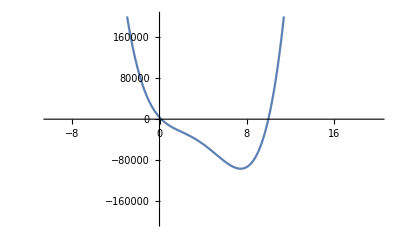

```mathematica
Plot[3645-23544*#1+7830*#1^2-1800*#1^3+125*#1^4&[x],{x,-10,20},PlotRange->{-200000,200000}]
```

```mathematica
?Roots
```

```mathematica
Roots[3645-23544*#1+7830*#1^2-1800*#1^3+125*#1^4&[x]==0,x]
```

x==18/5-3/5 √(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))-1/2 √(504/25+2484/(25 (-11+64 √3)^(1/3))-108/25 (-11+64 √3)^(1/3)-4608/(25 √(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))))||x==18/5-3/5 √(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))+1/2 √(504/25+2484/(25 (-11+64 √3)^(1/3))-108/25 (-11+64 √3)^(1/3)-4608/(25 √(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))))||x==18/5+3/5 √(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))-1/2 √(504/25+2484/(25 (-11+64 √3)^(1/3))-108/25 (-11+64 √3)^(1/3)+4608/(25 √(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))))||x==18/5+3/5 √(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))+1/2 √(504/25+2484/(25 (-11+64 √3)^(1/3))-108/25 (-11+64 √3)^(1/3)+4608/(25 √(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))))

```mathematica
18/5+3/5 √(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))-1/2 √(504/25+2484/(25 (-11+64 √3)^(1/3))-108/25 (-11+64 √3)^(1/3)+4608/(25 √(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))))//FullSimplify
```

3/5 Root0.272Root[225-872 #1+174 #1^2-24 #1^3+#1^4&,1]0.2722705545942298

```mathematica
3/5 Root"0.272"Root[225-872 #1+174 #1^2-24 #1^3+#1^4&,1]0.2722705545942298//InputForm
```

```mathematica
18/5+3/5 √(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))-1/2 √(504/25+2484/(25 (-11+64 √3)^(1/3))-108/25 (-11+64 √3)^(1/3)+4608/(25 √(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))))//Simplify
```

18/5+3/5 √(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))-1/2 √(504/25+2484/(25 (-11+64 √3)^(1/3))-108/25 (-11+64 √3)^(1/3)+4608/(25 √(7-69/(-11+64 √3)^(1/3)+3 (-11+64 √3)^(1/3))))

```mathematica
N[%320/2,10]
```

0.08168116638

```mathematica
%//RootReduce
```

x==Root2.12-3.65 ⅈRoot[3645-23544 #1+7830 #1^2-1800 #1^3+125 #1^4&,3]2.124819577019769||x==Root2.12+3.65 ⅈRoot[3645-23544 #1+7830 #1^2-1800 #1^3+125 #1^4&,4]2.124819577019769||x==Root0.163Root[3645-23544 #1+7830 #1^2-1800 #1^3+125 #1^4&,1]0.1633623327565379||x==Root9.99Root[3645-23544 #1+7830 #1^2-1800 #1^3+125 #1^4&,2]9.986998513203925

```mathematica
(U@@@(#[[1]]-#[[2]]&/@Subsets[coords,{2}]))/.ssol[[1]]//FullSimplify//Sort
```

{1/75 (11-4 √6),1/75 (11-4 √6),1/75 (11-4 √6),1/75 (11-4 √6),1/75 (11-4 √6),1/75 (11-4 √6),1/25 (-4+√6)^2,1/25 (-4+√6)^2,1/25 (-4+√6)^2,1/25 (-4+√6)^2}

```mathematica
u/.ssol[[1]]//FullSimplify
```

3-2 √2

```mathematica
u/.ssol[[2]]//FullSimplify
```

3-(3 √3)/2